# AntonAntonov/ClassifierEnsembles

Creation of- and classification with ensembles of classifiers

## Paclet Manifest

"Documentation"

"English"

"Guides"

"Ensemblesofclassifiers.nb"DocumentationEnglishGuidesEnsemblesofclassifiers.nb

"ReferencePages"

"Symbols"

"ClassifyByThreshold.nb"DocumentationEnglishReferencePagesSymbolsClassifyByThreshold.nb

"EnsembleClassifierConfusionMatrix.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierConfusionMatrix.nb

"EnsembleClassifierMeasurements.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierMeasurements.nb

"EnsembleClassifier.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifier.nb

"EnsembleClassifierProbabilities.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierProbabilities.nb

"EnsembleClassifierROCData.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierROCData.nb

"EnsembleClassifierROCPlots.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierROCPlots.nb

"EnsembleClassifierVotes.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierVotes.nb

"EnsembleClassifyByThreshold.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifyByThreshold.nb

"EnsembleClassify.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassify.nb

"ResamplingEnsembleClassifier.nb"DocumentationEnglishReferencePagesSymbolsResamplingEnsembleClassifier.nb

"Tutorials"

"ROCforclassifierensemblesbootstrappingdamagingandinterpolation.nb"DocumentationEnglishTutorialsROCforclassifierensemblesbootstrappingdamagingandinterpolation.nb

"Kernel"

"ClassifierEnsembles.wl"KernelClassifierEnsembles.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

Functions for creating Machine Learning classifier ensembles and making classifications using averaged probabilities, votes, and thresholds.

### Details

Classifier ensembles are Association objects that have Classify-made objects as values.

The function that makes classifier ensembles, EnsembleClassifier, can take data arguments that Classify can take.

Classifier creations using data resampling specifications can be made with ResamplingEnsembleClassifier.

A classifier ensemble is created with a list of names of the algorithms used by Classify.

Using Automatic all (relevant) classifier making algorithms for the given data are used.

A given record is classified by default using the average probabilities for the labels given by the classifiers.

A given record can be also classified by using the number of classifier votes for the labels.

Thresholds for the individual labels can be specified.

Ensemble classifier measurements can be computed with EnsembleClassifierMeasurements.

Ensemble classifier results can be processed and visualized with Reciever Operating Characteristic (ROC) functions of the paclet "ROCFunctions".

### Primary Context

AntonAntonov`ClassifierEnsembles`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`ClassifierEnsembles`"];
```

### Flowchart

Here is a flowchart that summarizes the classification process (made with Mermaid-JS):

```mathematica
ResourceFunction["MermaidInk"]["
graph TD
    A[\"Input Data (X1, X2, ..., Xn, Y)\"] --> B[NearestNeighbors]
    A --> C[NeuralNetwork]
    A --> D[LogisticRegression]
    A --> E[RandomForest]
    A --> F[SupportVectorMachine]
    A --> G[NaiveBayes]
    
    B --> H[Voting/Combination Mechanism]
    C --> H
    D --> H
    E --> H
    F --> H
    G --> H
    
    H --> I[Final Prediction]
"]
```

-Graphics-

### Basic Examples

Get training data:

```mathematica
data=ExampleData[{"MachineLearning","Titanic"},"TrainingData"];
data=((Flatten@*List)@@@data)[[All,{1,2,3,-1}]];
trainingData=DeleteCases[data,{___,_Missing,___}];
```

Get testing data:

```mathematica
data=ExampleData[{"MachineLearning","Titanic"},"TestData"];
data=((Flatten@*List)@@@data)[[All,{1,2,3,-1}]];
testData=DeleteCases[data,{___,_Missing,___}];
```

Summarize the training and testing data:

```mathematica
ResourceFunction["GridTableForm"][]
```

# | Data | Summary
1 | Training | {1 column 1
3rd | 354
1st | 197
2nd | 181,2 column 2
Min | 0.3333
1st Qu | 21.
Median | 27.
Mean | 29.4164
3rd Qu | 38.
Max | 80.,3 column 3
male | 460
female | 272,4 column 4
died | 427
survived | 305}
2 | Testing | {1 column 1
3rd | 147
1st | 87
2nd | 80,2 column 2
Min | 0.1667
1st Qu | 21.
Median | 30.
Mean | 30.9644
3rd Qu | 40.
Max | 76.,3 column 3
male | 198
female | 116,4 column 4
died | 192
survived | 122}

Create a classifier ensemble using Classify method names:

```mathematica
aCLs=EnsembleClassifier[{"LogisticRegression","NearestNeighbors","RandomForest","GradientBoostedTrees","NaiveBayes"},trainingData[[All,1;;-2]]->trainingData[[All,-1]]];
aCLs//Rasterize
```

-Graphics-

#### Classify a record

Classify a record with the ensemble:

```mathematica
EnsembleClassify[aCLs,testData[[4,1;;-2]]]
```

died

Classify a record using classifier votes and specifying 2 to be the threshold for the label "survived":

```mathematica
EnsembleClassifyByThreshold[aCLs,testData[[4,1;;-2]],"survived"->2,"Votes"]
```

died

Classify a record using the mean of the probabilities given by each classifier and a threshold for "survived":

```mathematica
EnsembleClassifyByThreshold[aCLs,testData[[4,1;;-2]],"survived"->0.2,"ProbabilitiesMean"]
```

survived

#### Classify a list of records using a threshold

Classify a list of records and return "survived" if it gets at least two votes:

```mathematica
EnsembleClassifyByThreshold[aCLs,testData[[1;;12,1;;-2]],"survived"->2,"Votes"]
```

{survived,died,survived,died,died,survived,died,survived,died,survived,died,survived}

Return "survived" if its average probability is at least 0.7:

```mathematica
EnsembleClassifyByThreshold[aCLs,testData[[1;;12,1;;-2]],"survived"->0.7,"ProbabilitiesMean"]
```

{survived,died,survived,died,died,survived,died,survived,died,survived,died,survived}

### Scope

#### Probabilities and votes

Get the probabilities:

```mathematica
EnsembleClassifierProbabilities[aCLs,testData[[4,1;;-2]]]
```

<|died→0.601325,survived→0.398675|>

Get the votes:

```mathematica
EnsembleClassifierVotes[aCLs,testData[[4,1;;-2]]]
```

<|died→4,survived→1|>

#### Classifier measurements

Compute classifier measurements:

```mathematica
measures={"Accuracy","Precision","Recall"};
EnsembleClassifierMeasurements[aCLs,Thread[testData⟦All,1;;-2⟧->testData⟦All,-1⟧],measures]//AssociationThread[measures,#]&
```

<|Accuracy→0.808917,Precision→<|died→0.817308,survived→0.792453|>,Recall→<|died→0.885417,survived→0.688525|>|>

#### Threshold classification with ROC

Compute Receiver Operating Characteristic (ROC) for a range of thresholds for the label "survived" (using the paclet "ROCFunctions"):

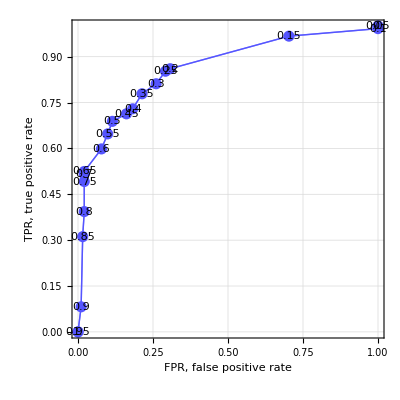

```mathematica
rocRange=Range[0,1,0.05];
aROCs=Table[(cres=EnsembleClassifyByThreshold[aCLs,testData[[All,1;;-2]],"survived"->i];
{{-Graphics-, ToROCAssociation}}[{"survived","died"},testData[[All,-1]],cres]),{i,rocRange}];
{{-Graphics-, ROCPlot}}[rocRange,aROCs,GridLines->Automatic]
```

#### Data

EnsembleClassifier can take data arguments that Classify can take. Here is a Dataset object for the built-in Titanic data:

```mathematica
dsTitanic=ResourceFunction["ExampleDataset"][{"MachineLearning","Titanic"}];
```

Here we split that Dataset object into two (training and testing):

```mathematica
{dsTraining,dsTesting}=TakeDrop[RandomSample[dsTitanic],Length[dsTitanic]*0.8//Floor];
ResourceFunction["RecordsSummary"]/@{dsTraining,dsTesting}
```

{{1 passenger class
3rd | 560
1st | 265
2nd | 222,2 passenger age
Min | 0.1667
1st Qu | 21.
Median | 28.
Mean | 29.967
3rd Qu | 39.
Max | 76.
Missing[___] | 200,3 passenger sex
male | 670
female | 377,4 passenger survival
died | 649
survived | 398},{1 passenger class
3rd | 149
1st | 58
2nd | 55,2 passenger age
Min | 0.75
1st Qu | 21.25
Median | 28.
Mean | 29.5155
3rd Qu | 36.875
Max | 80.
Missing[___] | 63,3 passenger sex
male | 173
female | 89,4 passenger survival
died | 160
survived | 102}}

Here we make a classifier ensemble with the training dataset:

```mathematica
aCLs2=EnsembleClassifier[{"LogisticRegression","RandomForest"},dsTraining[All,1;;-2]->dsTraining[[All,-1]]]
```

<|LogisticRegression→ClassifierFunction[…],RandomForest→ClassifierFunction[…]|>

Here we classify the records of the testing dataset:

```mathematica
new=EnsembleClassify[aCLs2,Normal@dsTesting[All,1;;-2]];
new//Shallow
```

{died,died,died,died,died,died,died,died,survived,died,«252»}

#### Confusion matrix

Confusion matrix can be computed and plotted using functions of the paclet "ROCFunctions". Here is an example:

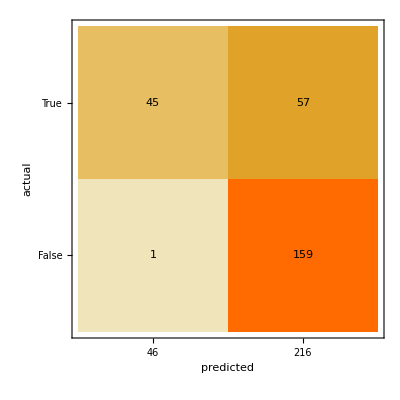

```mathematica
{{-Graphics-, ConfusionMatrixPlot}}[{{-Graphics-, ToROCAssociation}}[{"survived","died"},Normal@dsTesting[[All,-1]],new]]
```

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-ClassifierEnsembles-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Classification

Classifier

Ensemble

Classifier ensemble

ROC functions

Machine Learning

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

AntonAntonov/DataReshapers

AntonAntonov/ROCFunctions

ExampleDataset

RecordsSummary

GridTableForm

### Original Source References and Attributions

ROC for classifier ensembles, bootstrapping, damaging, and interpolation | Mathematica for prediction algorithms

### Links

MathematicaForPrediction/ClassifierEnsembles.m at master · antononcube/MathematicaForPrediction · GitHub

### Compatibility

#### Wolfram Language Version

12.1+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.